# System size effect for diffusion constants

### data loading

```mathematica
sizes={32768,4096,512,128};
```

```mathematica
p0s={3.85,3.75};
```

```mathematica
temperatures={0.002,0.02};
 records={Table[i,{i,0,9}],Table[i,{i,10,19}],Table[i,{i,0,9}],Table[i,{i,0,9}]};
```

```mathematica
If[sizes[[2]]==4096,records[[1]]+10,records[[1]]]
```

{10,11,12,13,14,15,16,17,18,19}

```mathematica
trueMSDs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N","/tauAlphaData/p","/timeTrueMSD_N","_p","_T","_waitingTime10000_idx",".nc"},{sizes[[n]],p0s[[p]],sizes[[n]],p0s[[p]],temperatures[[p]],records[[n,i]]},{0,3,0,4,8,0}],"Data"],{i,Length[records[[n]]]}],$Failed],{n,Length[sizes]}],{p,Length[p0s]}];
```

```mathematica
trueCRMSDs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N","/tauAlphaData/p","/timeTrueCRMSD_N","_p","_T","_waitingTime10000_idx",".nc"},{sizes[[n]],p0s[[p]],sizes[[n]],p0s[[p]],temperatures[[p]],records[[n,i]]},{0,3,0,4,8,0}],"Data"],{i,Length[records[[n]]]}],$Failed],{n,Length[sizes]}],{p,Length[p0s]}];
```

```mathematica
diffusionConstants=Table[Table[Table[trueMSDs[[p,n,i,2,Length[trueMSDs[[p,n,i,2]]]]]/4/(trueMSDs[[p,n,i,1,Length[trueMSDs[[p,n,i,1]]]]]),{i,10}],{n,Length[sizes]}],{p,Length[p0s]}]
```

{{{0.00127486,0.00159844,0.00147105,0.00127201,0.00153234,0.00165264,0.00179135,0.00153257,0.00148338,0.00181117},{0.00120896,0.00117582,0.00135036,0.00106751,0.000934697,0.00114519,0.00106171,0.00107043,0.00129801,0.000950025},{0.000834266,0.00104652,0.00101133,0.000830746,0.00105745,0.00101399,0.00110211,0.000694483,0.000875467,0.000994237},{0.00083664,0.00060171,0.000622219,0.000528006,0.000556989,0.000668403,0.000756395,0.000903024,0.000695096,0.00086735}},{{0.00459171,0.00463269,0.00485236,0.00555171,0.00521094,0.00466186,0.00462126,0.00448841,0.00528742,0.00464963},{0.00373171,0.00381979,0.00375119,0.00467111,0.00432836,0.00399193,0.00438199,0.00407034,0.003873,0.00366837},{0.0029006,0.00322331,0.00333657,0.00286406,0.00271404,0.00300114,0.00289505,0.00292971,0.00327988,0.00363472},{0.00227762,0.00265034,0.0021675,0.00220802,0.00202282,0.00250959,0.00225581,0.00245711,0.0025982,0.00228275}}}

```mathematica
diffusionConstantsCR=Table[Table[Table[trueCRMSDs[[p,n,i,2,Length[trueCRMSDs[[p,n,i,2]]]]]/4/(trueCRMSDs[[p,n,i,1,Length[trueCRMSDs[[p,n,i,1]]]]]),{i,10}],{n,Length[sizes]}],{p,Length[p0s]}]
```

{{{0.000882885,0.000869138,0.000859329,0.000863193,0.000871509,0.000871198,0.000883889,0.000884411,0.000886333,0.000863206},{0.000888648,0.000901008,0.000902884,0.000854252,0.000852659,0.000940576,0.000865142,0.000873203,0.000885534,0.000832482},{0.000868727,0.00101209,0.000896872,0.00074965,0.000886311,0.000817277,0.000856973,0.000748115,0.000864649,0.00087558},{0.000922139,0.00062662,0.000683103,0.000596407,0.000536172,0.000666103,0.000790938,0.000892417,0.000752539,0.000929667}},{{0.00358092,0.00360821,0.00365855,0.0036607,0.00359425,0.00359011,0.00362088,0.00360904,0.0035665,0.00361497},{0.00344757,0.00349781,0.00337658,0.00381636,0.00381739,0.0035285,0.00360638,0.00359884,0.00353281,0.00327157},{0.0031488,0.0034002,0.00343309,0.0029342,0.00307527,0.00320365,0.00338961,0.00313189,0.00348836,0.00381381},{0.00241217,0.00294797,0.00258005,0.00245292,0.00223154,0.00284303,0.00261191,0.0026919,0.00254462,0.00248242}}}

```mathematica
meanCRD=Table[Table[Mean[Table[diffusionConstantsCR[[p,n,i]],{i,10}]],{n,Length[sizes]}],{p,Length[p0s]}]
```

{{0.000873509,0.000879639,0.000857624,0.000739611},{0.00361041,0.00354938,0.00330189,0.00257985}}

```mathematica
meanD=Table[Table[Mean[Table[diffusionConstants[[p,n,i]],{i,10}]],{n,Length[sizes]}],{p,Length[p0s]}]
```

{{0.00154198,0.00112627,0.000946061,0.000703583},{0.0048548,0.00402878,0.00307791,0.00234298}}

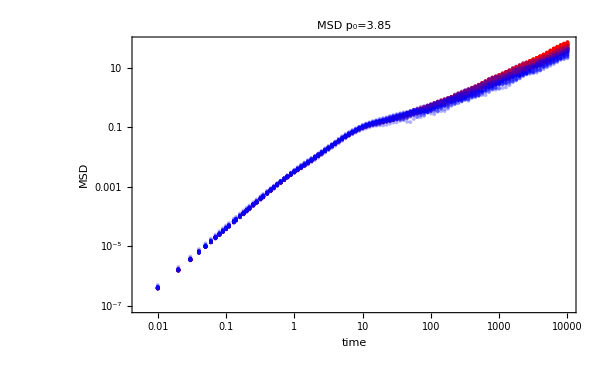
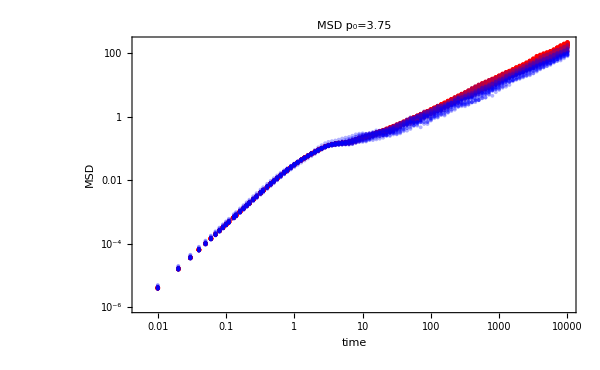

```mathematica
Table[Show[Table[ListLogLogPlot[Table[Table[{trueMSDs[[p,n,i,1,t]],trueMSDs[[p,n,i,2,t]]},{t,Length[trueMSDs[[p,n,i,1]]]}],{i,10}],ImageSize->600,PlotLabel->"MSD p_0="<>ToString[p0s[[p]]],FrameLabel->{"time","MSD"},PlotStyle->redBluePlotConfig[4][[n]]],{n,Length[sizes]}]],{p,Length[p0s]}]
```

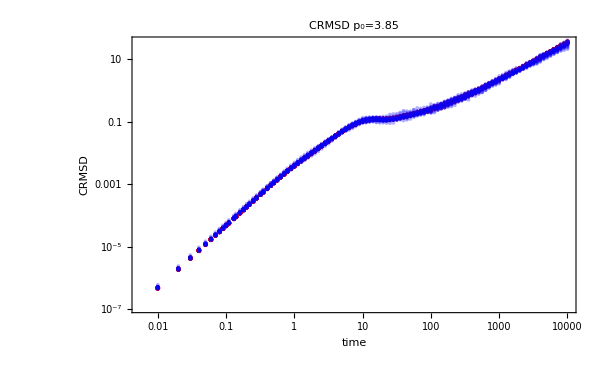
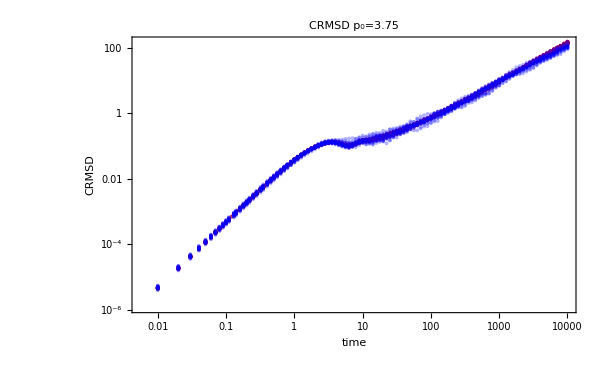

```mathematica
Table[Show[Table[ListLogLogPlot[Table[Table[{trueCRMSDs[[p,n,i,1,t]],trueCRMSDs[[p,n,i,2,t]]},{t,Length[trueCRMSDs[[p,n,i,1]]]}],{i,10}],ImageSize->600,PlotLabel->"CRMSD p_0="<>ToString[p0s[[p]]],FrameLabel->{"time","CRMSD"},PlotStyle->redBluePlotConfig[4][[n]]],{n,Length[sizes]}]],{p,Length[p0s]}]
```

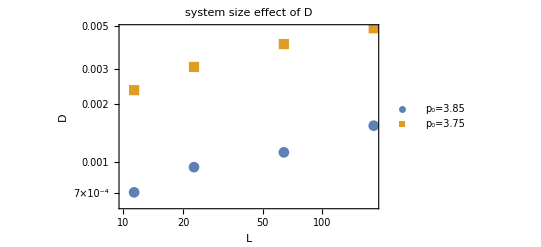

```mathematica
ListLogLogPlot[Table[Table[{Sqrt[sizes[[n]]],meanD[[p,n]]},{n,Length[sizes]}],{p,Length[p0s]}],ImageSize->400,PlotLabel->"system size effect of D",FrameLabel->{"L","D"}, PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],PlotMarkers->Automatic]
```

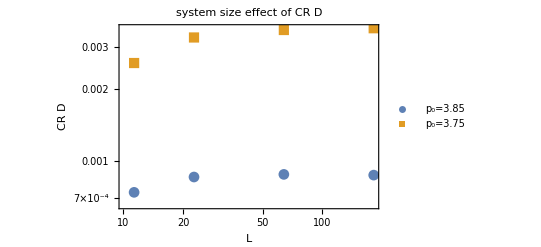

```mathematica
ListLogLogPlot[Table[Table[{Sqrt[sizes[[n]]],meanCRD[[p,n]]},{n,Length[sizes]}],{p,Length[p0s]}],ImageSize->400,PlotLabel->"system size effect of CR D",FrameLabel->{"L","CR D"}, PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],PlotMarkers->Automatic]
```